### Initialization

```mathematica
<<NCAlgebra`
<<NCGBX`
```

------------------------------------------------------------

NCAlgebra - Version 6.0.3

Compatible with Mathematica Version 10 and above



Authors:



  J. William Helton*

  Mauricio de Oliveira&



* Math, UCSD, La Jolla, CA

& MAE, UCSD, La Jolla, CA



with major earlier contributions by:



  Mark Stankus$ 

  Robert L. Miller#



$ Math, Cal Poly San Luis Obispo

# General Atomics Corp



Copyright: 

  Helton and de Oliveira 2023

  Helton and de Oliveira 2017

  Helton 2002

  Helton and Miller June 1991

  All rights reserved.



The program was written by the authors and by:

  David Hurst, Daniel Lamm, Orlando Merino, Robert Obar,

  Henry Pfister, Mike Walker, John Wavrik, Lois Yu,

  J. Camino, J. Griffin, J. Ovall, T. Shaheen, John Shopple. 

  The beginnings of the program come from eran@slac.

  Considerable recent help came from Igor Klep.



Current primary support is from the 

  NSF Division of Mathematical Sciences.

  

This program was written with support from 

  AFOSR, NSF, ONR, Lab for Math and Statistics at UCSD,

  UCSD Faculty Mentor Program,

  and US Department of Education.



For NCAlgebra updates see:



  www.github.com/NCAlgebra/NC

  www.math.ucsd.edu/~ncalg



------------------------------------------------------------

NCAlgebra::SmallCapSymbolsNonCommutative: All lower cap single letter symbols (e.g. a,b,c,...) were set as noncommutative.

### Classical mutations

The function μ takes as input a list Z with two elements: the cluster variables  X and the exchange matrix B. The index k specifies which cluster variable to mutate. The function returns a new list containing the updated cluster variables and exchange matrix after mutation. Moreover, the function ExchangeMatrixQuiver generates the sl2 quiver associated to the n-punctured disk.

```mathematica
Subscript[μ, k_][Z_]:=Module[{X,B,n},{X,B}=Z;
n=Length[X];
{Table[If[i==k,X[[i]]^-1,X[[i]] (1+X[[k]]^(-Sign[B[[k,i]]]))^(-B[[k,i]])],{i,n}],
Table[If[i==k||j==k,-B[[i,j]],B[[i,j]]+(B[[i,k]] Abs[B[[k,j]]]+Abs[B[[i,k]]] B[[k,j]])/2],{i,n},{j,n}]}]
Quiver[Z_]:=AdjacencyGraph[(Z+ Transpose[Abs[Z]])/2,VertexLabels->Automatic];
QuiverEdges[n_]:=Flatten@Table[With[{b=3 k+1},{b->b+1,b+1->b+3,b+3->b+2,b+2->b}],{k,0,n-1}];
ExchangeMatrixQuiver[n_]:=Module[{Nverts,edges,pos},Nverts=3 n+1;
edges=QuiverEdges[n];
pos=(List@@#)&/@edges;(*list of {u,v}*)SparseArray[Join[(#->1)&/@pos,(Reverse[#]->-1)&/@pos],{Nverts,Nverts}]];
σ[n_,i_,j_]:=Module[{I},I=IdentityMatrix[n];
I[[All,{i,j}]]=I[[All,{j,i}]];
I];
M[n_,i_]:=σ[3n+1,3i,3i+2].σ[3n+1,3i-1,3i+2].σ[3n+1,3i,3i+3]
B=ExchangeMatrixQuiver[2]//Normal;
V=Table[Subscript[v, i],{i,1,7}];
Rgen[V_,B_,n_,i_]:= Module[{M= M[n,i]},{M.#1,M.#2.Transpose[M]}&@@({V,B}//Subscript[μ, 3i+1]//Subscript[μ, 3i+3]//Subscript[μ, 3i-1]//Subscript[μ, 3i+1])]
Rgeninv[V_,B_,n_,i_]:= Module[{M= σ[3n+1,3i,3i+3].σ[3n+1,3i-1,3i+2].σ[3n+1,3i,3i+2]},{M.#1,M.#2.Transpose[M]}&@@({V,B}//Subscript[μ, 3i+1]//Subscript[μ, 3i]//Subscript[μ, 3i+2]//Subscript[μ, 3i+1])]

R[V_,B_]:=Rgen[V,B,2,1]
ClusterVar[n_]:=Table[Which[i==1,I T^-1 Subscript[x, 1],i==2,-T^2,i==3,-1,i==3 n+1,I Subscript[x, n]^-1,Mod[i,3]==1,-T^-1 Subscript[x, (i-1)/3]^-1 Subscript[x, (i+2)/3],Mod[i,3]==2,-T^2,Mod[i,3]==0,-1],{i,1,3 n+1}];
```

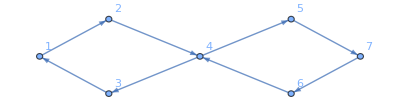

```mathematica
B//Quiver
```

```mathematica
R[V,B][[1]]
```

{v_1 (1+v_2 (1+v_4)),v_5/((1+1/v_4) (1+1/(v_2 (1+v_4))) (1+1/((1+v_4) v_6)) (1+v_4/((1+v_2 (1+v_4)) (1+(1+v_4) v_6)))),(1+((1+v_2 (1+v_4)) (1+(1+v_4) v_6))/v_4)/(v_2 (1+v_4)),v_4/((1+v_2 (1+v_4)) (1+(1+v_4) v_6)),(1+((1+v_2 (1+v_4)) (1+(1+v_4) v_6))/v_4)/((1+v_4) v_6),v_3/((1+1/v_4) (1+1/(v_2 (1+v_4))) (1+1/((1+v_4) v_6)) (1+v_4/((1+v_2 (1+v_4)) (1+(1+v_4) v_6)))),(1+(1+v_4) v_6) v_7}

### Example Trefoil

Applying the R-matrix operator three times yields cluster variables associated to the trefoil.

```mathematica
R@@R@@R[{Subscript[x, 1] T^-1,-T^2,-1,T^-1 Subscript[x, 1]^-1 Subscript[x, 2],-T^2,-1,Subscript[x, 2]^-1},B]//FullSimplify
```

{{-x_2-((-1+T^2) ((1+T^4) x_1+T^3 x_2))/T,-T^2,-1,((1-T^2+T^4) x_1+T (-1+T^2) x_2)/((-1+T) (1+T) (1+T^4) x_1+T (1-T^2+T^4) x_2),-T^2,-1,-1/(T ((1-T^2+T^4) x_1+T (-1+T^2) x_2))},{{0,1,-1,0,0,0,0},{-1,0,0,1,0,0,0},{1,0,0,-1,0,0,0},{0,-1,1,0,1,-1,0},{0,0,0,-1,0,0,1},{0,0,0,1,0,0,-1},{0,0,0,0,-1,1,0}}}

### Example figure 8

```mathematica
B3=ExchangeMatrixQuiver[3]//Normal;
```

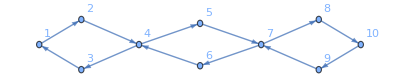

```mathematica
B3//Quiver
```

```mathematica
W=ClusterVar[3]
```

{(ⅈ x_1)/T,-T^2,-1,-x_2/(T x_1),-T^2,-1,-x_3/(T x_2),-T^2,-1,ⅈ/x_3}

```mathematica
Subscript[R3, k_][V_,B_]:=Rgen[V,B,3,k]//FullSimplify
Subscript[R3inv, k_][V_,B_]:=Rgeninv[V,B,3,k]//FullSimplify
```

```mathematica
(Subscript[R3inv, 2]@@Subscript[R3, 1]@@Subscript[R3inv, 2]@@(Subscript[R3, 1][W,B3]))[[1]]
```

{(ⅈ ((-1+T^2)^2 x_1+(T-T^3) x_2+x_3))/T,-T^2,-1,(x_3-T^2 (x_1+x_3))/(T^4 ((-1+T^2)^2 x_1+(T-T^3) x_2+x_3)),-T^2,-1,-1+1/T^2+(T^2 ((-1+T^2) x_1-T x_2))/(T^2 x_1+(-1+T^2) x_3),-T^2,-1,-(ⅈ T^4)/(T^2 (-1+T^2)^2 x_1-T^5 x_2-(-1+T^2)^2 x_3)}

### Quantum Mutations

```mathematica
Subscript[μq, k_][Z_]:=Module[{X,B,n},{X,B}=Z ; n=Length[X];{Table[If[i==k,inv[X[[k]]],If[B[[k,i]]>=0,X[[i]]**Product[inv[(1+q^(2m-1)inv[X[[k]]])],{m,1,B[[k,i]]}],X[[i]]**Product[(1+q^(2m-1)X[[k]]),{m,1,-B[[k,i]]}]]],{i,1,n}],Table[Table[If[i==k || j==k,-B[[i,j]],B[[i,j]]+(B[[i,k]]Abs[B[[k,j]]] + Abs[B[[i,k]]]B[[k,j]])/2],{j,1,n}],{i,1,n}]}]

 Rq[V_,B_]:=Module[{M= M[2,1]},{M.#1,M.#2.Transpose[M]}&@@({V,B}//Subscript[μq, 4]//Subscript[μq, 6]//Subscript[μq, 2]//Subscript[μq, 4])]
```

```mathematica
Rq[V,B][[1,1]]
```

v_1**(1+q v_2**(1+q v_4))

```mathematica
Rq[V,B][[1,7]]
```

v_7**(1+q v_6**(1+q v_4))

### Relations

Let us start by initializing the relations within the package NCAlgebra, as shown below. To do this, we need to define the commutative and non-commutative variables. Among the non-commutative variables, an order needs to be specified. The array RelsHB specifies the relations of the Weyl-Heisenberg algebra. The array RelsQT specifies the relations of the quantum torus algebra. Note that Z_i = inv Y_i. Lastly, gbqt and gbhb produces a Gröbner basis associated to the list of polynomials RelsQT and RelsHB, respectively. The NCMakeGB algorithm performs at most k iterations to compute a Gröbner basis for the input list of polynomials, relative to the monomial order.

```mathematica
SetCommutative[q,ϵ];
SetNonCommutative[x,y,Y,Z];
SetMonomialOrder[Subscript[x, 1],Subscript[x, 1]^-1,Subscript[x, 2],Subscript[x, 2]^-1,Subscript[p, 1],Subscript[p, 2],Subscript[Y, 1],Subscript[Y, 2],Subscript[Z, 1],Subscript[Z, 2]];
Rels[n_]:= {Subscript[x, 1] ** Subscript[Y, 1] -q^-n Subscript[Y, 1] **Subscript[x, 1], Subscript[x, 1] **Subscript[x, 2]-Subscript[x, 2]**Subscript[x, 1],Subscript[Y, 1]**Subscript[Y, 2]-Subscript[Y, 2]**Subscript[Y, 1], Subscript[x, 1]**Subscript[Y, 2]-Subscript[Y, 2]**Subscript[x, 1], Subscript[x, 2]**Subscript[Y, 1]-Subscript[Y, 1]**Subscript[x, 2], Subscript[x, 2] **Subscript[Y, 2]-q^-n Subscript[Y, 2]**Subscript[x, 2]};
RelsQT=Rels[1]∪ (Rels[-1]/.{Subscript[Y, 1]->Subscript[Z, 1],Subscript[Y, 2]->Subscript[Z, 2]})∪{Subscript[Z, 1]**Subscript[Y, 1]-Subscript[Y, 1]**Subscript[Z, 1], Subscript[Z, 1]**Subscript[Y, 2]-Subscript[Y, 2]**Subscript[Z, 1], Subscript[Z, 2]**Subscript[Y, 1]-Subscript[Y, 1]**Subscript[Z, 2],Subscript[Z, 2]**Subscript[Y, 2]-Subscript[Y, 2]**Subscript[Z, 2]};
RelsHB = {Subscript[p, 1]**Subscript[x, 1]-Subscript[x, 1]**Subscript[p, 1]-1,Subscript[p, 2]**Subscript[x, 2]-Subscript[x, 2]**Subscript[p, 2]-1,Subscript[x, 1]**Subscript[x, 2]-Subscript[x, 2]**Subscript[x, 1],Subscript[p, 1]**Subscript[p, 2]-Subscript[p, 2]**Subscript[p, 1],Subscript[x, 1]**Subscript[p, 2]-Subscript[p, 2]**Subscript[x, 1],Subscript[x, 2]**Subscript[p, 1]-Subscript[p, 1]**Subscript[x, 2]};
gbqt=NCMakeGB[RelsQT,10];
gbhb= NCMakeGB[RelsHB,10];
```

* * * * * * * * * * * * * * * *

* * *   NCPolyGroebner    * * *

* * * * * * * * * * * * * * * *

* Symbolic coefficients detected

* Monomial order:

> x_1≪ (x
 1)^-1≪ x_2≪ (x
 2)^-1≪ p_1≪ p_2≪ Y_1≪ Y_2≪ Z_1≪ Z_2

* Reduce and normalize initial set

> Initial set could not be reduced

* Computing initial set of obstructions

> MAJOR Iteration 1, 29 polys in the basis, 71 obstructions

> MAJOR Iteration 2, 33 polys in the basis, 87 obstructions

> MAJOR Iteration 3, 32 polys in the basis, 58 obstructions

> MAJOR Iteration 4, 31 polys in the basis, 22 obstructions

> MAJOR Iteration 5, 30 polys in the basis, 6 obstructions

* Found Groebner basis with 30 polynomials

* * * * * * * * * * * * * * * *

* * * * * * * * * * * * * * * *

* * *   NCPolyGroebner    * * *

* * * * * * * * * * * * * * * *

* Monomial order:

> x_1≪ (x
 1)^-1≪ x_2≪ (x
 2)^-1≪ p_1≪ p_2≪ Y_1≪ Y_2≪ Z_1≪ Z_2

* Reduce and normalize initial set

> Initial set could not be reduced

* Computing initial set of obstructions

> MAJOR Iteration 1, 16 polys in the basis, 31 obstructions

> MAJOR Iteration 2, 16 polys in the basis, 23 obstructions

> MAJOR Iteration 3, 16 polys in the basis, 14 obstructions

> MAJOR Iteration 4, 18 polys in the basis, 13 obstructions

> MAJOR Iteration 5, 17 polys in the basis, 4 obstructions

* Found Groebner basis with 17 polynomials

* * * * * * * * * * * * * * * *

### Input and functions

This list input defines the quantum cluster variables as in (6.2). The function NormalOrder normal orders exponents in accordance with Proposition 3.5. The function ExpandExponents merely expands exponents, without placing them in a normal ordered format. The function P interchanges tensor factors. NCIntp provides functionality for integrating expressions involving Heisenberg operators with respect to the variables p_i.

```mathematica
$k=2;
input={I Subscript[x, 1] T^-1,- q T^2 Subscript[Y, 1]^2 ,-q^-1 Subscript[Z, 1]^2,- T^-1 Subscript[x, 1]^-1**Subscript[x, 2]  ,- q T^2 Subscript[Y, 1]^2 ,-q^-1 Subscript[Z, 2]^2,I Subscript[x, 2]^-1} ;
NormalOrder[F_]:= ((Expand[F]/.{Subscript[Z, 1]^n_->Subscript[Y, 1]^-n,Subscript[Z, 2]^n_->Subscript[Y, 2]^-n})/.{Subscript[Y, k_]^n_->Sum[((q^n-1)^i Subscript[x, k]^i**Subscript[p, k]^i)/(i!),{i,0,$k}]});
ExpandExponents[F_]:=(Expand[F]/.{Subscript[Z, 1]^n_->Subscript[Y, 1]^-n,Subscript[Z, 2]^n_->Subscript[Y, 2]^-n})/.{Subscript[Y, 1]^n_-> Sum[(n ϵ Subscript[x, 1]**Subscript[p, 1])^k/(k!),{k,0,$k}],Subscript[Y, 2]^n_->Sum[(n ϵ Subscript[x, 2]**Subscript[p, 2])^k/(k!),{k,0,$k}],Subscript[Y, 1]-> Sum[(ϵ Subscript[x, 1]**Subscript[p, 1])^k/(k!),{k,0,$k}],Subscript[Y, 2]-> Sum[(ϵ Subscript[x, 2]**Subscript[p, 2])^k/(k!),{k,0,$k}]}
P[F_]:=Expand[F]/.{Subscript[x, 1]->Subscript[x, 2],Subscript[x, 2]->Subscript[x, 1],Subscript[p, 1]->Subscript[p, 2],Subscript[p, 2]->Subscript[p, 1]}
ApplyR0[F_]:=Expand[F]/.{Subscript[x, 1]->T^-1 Subscript[x, 1]+(1-T^-2)Subscript[x, 2],Subscript[x, 2]->T^-1 Subscript[x, 2],Subscript[p, 1]->T Subscript[p, 1],Subscript[p, 2]->(1-T^2)Subscript[p, 1]+T Subscript[p, 2]}
NCIntp[F_,i_] := NCExpandReplaceRepeated[NCExpand[F**Subscript[p, i]],gbhb]/.{Subscript[p, i]^n_-> 1/n Subscript[p, i]^n}
```

### Computing the perturbed R-matrix

```mathematica
img =Import["mathtext.pdf",{"PageImages",1},ImageResolution->300];
Image[img,ImageSize->Scaled[0.5]]
```

-Graphics-

```mathematica
NCSeries[f_,{x_,x0_,n_}]:=Block[{H},SetNonCommutative[H];
Plus@@(Table[1/i!,{i,0,n}]*NestList[NCDirectionalD[#,{x,H}]&,f,n])/. x->x0/. H->x]
Subscript[F, 1]:=-I*T*Rq[input,B][[1,1]]//NCExpandReplaceRepeated[#,gbqt]&//NormalOrder//NCExpand//ReplaceAll[#,q->Exp[ϵ]]&//Series[#,{ϵ,0,2}]&//Normal//P//ApplyR0//NCExpandReplaceRepeated[#,gbhb]&
Subscript[F, 2]:=-I*Rq[input,B][[1,7]]//NCExpandReplaceRepeated[#,gbqt]&//ReplaceAll[#,q->Exp[ϵ]]&//ExpandExponents//inv//NCSeries[#,{ϵ,0,2}]&//Normal//P//ApplyR0//NCExpandReplaceRepeated[#,gbhb]&
{Subscript[f, 1],Subscript[f, 2]} = Module[{Cof,IntCof},
Subscript[Cof, 1,1] = Coefficient[Subscript[F, 1],ϵ,1];
Subscript[Cof, 2,1]= Coefficient[Subscript[F, 2],ϵ,1];
Subscript[Cof, 1,2] = Coefficient[Subscript[F, 1],ϵ,2];
Subscript[Cof, 2,2]= Coefficient[Subscript[F, 2],ϵ,2];
Subscript[IntCof, 1,1] = NCIntp[Subscript[Cof, 1,1],1];
Subscript[f, 1] =NCIntp[Subscript[Cof, 2,1]-D[NCIntp[Subscript[Cof, 1,1],1],Subscript[p, 2]],2] +Subscript[IntCof, 1,1];
Subscript[Corr, 1]= NCExpandReplaceRepeated[Subscript[f, 1]**Subscript[Cof, 1,1]-Subscript[Cof, 1,1]**Subscript[f, 1],gbhb];Subscript[Corr, 2]= NCExpandReplaceRepeated[Subscript[f, 1]**Subscript[Cof, 2,1]-Subscript[Cof, 2,1]**Subscript[f, 1],gbhb];
Subscript[f, 2]=NCIntp[Subscript[Cof, 1,2] -(1/2)Subscript[Corr, 1],1];
{Subscript[f, 1],Subscript[f, 2]}
];
Subscript[Pert, i_,j_]=NCExpandReplaceRepeated[Sum[ϵ^n/(n!)(Subscript[f, 1]+ϵ Subscript[f, 2])^n+O[ϵ]^3,{n,0,2}],gbhb]/. {Subscript[x, 1]->T Subscript[x, i]+Subscript[x, j](1-T^2),Subscript[x, 2]->T Subscript[x, j],Subscript[p, 1]->Subscript[y, i],Subscript[p, 2]->Subscript[y, j],NonCommutativeMultiply->Times};
Subscript[InvPert, i_,j_]=NCExpandReplaceRepeated[Sum[(-ϵ)^n/(n!)(Subscript[f, 1]+ϵ Subscript[f, 2])^n+O[ϵ]^3,{n,0,2}]//NCExpand,gbhb]/. {Subscript[x, 1]->Subscript[x, i],Subscript[x, 2]->Subscript[x, j],Subscript[p, 1]->T^-1 Subscript[y, i],Subscript[p, 2]->(1-T^-2)Subscript[y, i]+T^-1 Subscript[y, j],NonCommutativeMultiply->Times};
```

### The contraction formalism

This code represents the contraction formalism taken from www.rolandvdv.nl/PG.

```mathematica
$k=2;(*Compute Z up to order $k in ϵ. Optional: set $k=1*);
{SuperStar[t],SuperStar[b],SuperStar[y],SuperStar[a],SuperStar[x],SuperStar[z]}={τ,β,η,α,ξ,ζ}; (*Variables and canonical form*)
{SuperStar[τ],SuperStar[β],SuperStar[η],SuperStar[α],SuperStar[ξ],SuperStar[ζ]}={t,b,y,a,x,z}; SuperStar[(Subscript[u_, i_])]:=Subscript[(SuperStar[u]), i];
U2l={Subscript[B, i_]^(p_.):>ⅇ^(-p ℏ  Subscript[b, i]),B^(p_.):>ⅇ^(-p ℏ  b), Subscript[T, i_]^(p_.):>ⅇ^(-p ℏ Subscript[t, i]),T^(p_.):>ⅇ^(-p ℏ t),Subscript[𝒜, i_]^(p_.):>ⅇ^(p  Subscript[α, i]),𝒜^(p_.):>ⅇ^(p  α)}; 
l2U={ⅇ^(c_. Subscript[b, i_]+d_.):>Subscript[B, i]^(-c/ℏ)ⅇ^d,ⅇ^(c_.b+d_.):>B^(-c/ℏ)ⅇ^d,ⅇ^(c_. Subscript[t, i_]+d_.):>Subscript[T, i]^(-c/ℏ)ⅇ^d,ⅇ^(c_.t+d_.):>T^(-c/ℏ)ⅇ^d,
ⅇ^(c_. Subscript[α, i_]+d_.):>Subscript[𝒜, i]^c ⅇ^d,ⅇ^(c_.α+d_.):>𝒜^c ⅇ^d,ⅇ^ℰ_:>ⅇ^(Expand@ℰ)};
CCF[ℰ_] := ExpandDenominator@ExpandNumerator@Together[
Expand[ℰ] //. ⅇ^x_ ⅇ^y_:>ⅇ^(x+y) /. ⅇ^x_:>ⅇ^CCF[x]];
CF[ℰ_List]:=CF/@ℰ;CF[sd_SeriesData] := MapAt[CF,sd,3];
CF[ℰ_] := Module[
{vs=Cases[ℰ,Subscript[(y|b|t|a|x|η|β|τ|α|ξ), _],∞]∪{y,b,t,a,x,η,β,τ,α,ξ}},
Total[CoefficientRules[Expand[ℰ], vs] /. (ps_->c_) :> CCF[c](Times@@(vs^ps))]];
CF[ℰ_𝔼]:=CF/@ℰ;CF[Subscript[𝔼, sp___][ℰs___]]:=CF/@Subscript[𝔼, sp][ℰs];
SetAttributes[Define, HoldAll] (*Define[lhs=rhs, ...]defines the lhs to be rhs,except that rhs is computed only once for each value of $k.*)
Define[def_,defs__] := (Define[def]; Define[defs];);
Define[Subscript[op_, is__]=ℰ_] := Module[{SD,ii,jj,kk,isp,nis,nisp,sis},Block[{i,j,k},
ReleaseHold[Hold[SD[Subscript[op, nisp,$k_Integer],Block[{i,j,k},Subscript[op, isp,$k]=ℰ;Subscript[op, nis,$k]]];
SD[Subscript[op, isp],Subscript[op, {is},$k]]; SD[Subscript[op, sis__],Subscript[op, {sis}]];]/. {SD->SetDelayed,
isp->{is}/.{i->i_,j->j_,k->k_},nis->{is}/.{i->ii,j->jj,k->kk},
nisp->{is}/.{i->ii_,j->jj_,k->kk_}}]  ]]
𝔼/:𝔼[G1_,P1_]≡𝔼[G2_,P2_]:=CF[G1==G2]∧CF[Normal[P1-P2]==0]; 
𝔼/:𝔼[G1_,P1_]𝔼[G2_,P2_]:=𝔼[G1+G2,P1*P2];(*Perturbed Gaussians*)
Subscript[𝔼[G_,P_], $k_]:=𝔼[G,Series[Normal@P,{ϵ,0,$k}]];
Subscript[𝔼, d1_->r1_][G1_,P1_]//Subscript[𝔼, d2_->r2_][G2_,P2_] :=
 Module[{n,is=r1∩d2},Subscript[𝔼, (d1∪Complement[d2,is])->(r2∪Complement[r1,is])]@@ (
((𝔼[G1,P1]/.Table[Subscript[(v:b|t|a|x|y), i]->Subscript[v, n@i],{i,is}])(𝔼[G2,P2]/.Table[Subscript[(v:β|τ|α|ξ|η), i]->Subscript[v, n@i],{i,is}]))
 // Subscript[Contract, Join@@Table[{Subscript[β, n@i],Subscript[τ, n@i],Subscript[a, n@i]},{i,is}]] // Subscript[Contract, Join@@Table[{Subscript[ξ, n@i],Subscript[y, n@i]},{i,is}]] )];
Subscript[𝔼, d1_->r1_][G1_,P1_]≡Subscript[𝔼, d2_->r2_][G2_,P2_] ^:= (d1==d2)∧(r1==r2)∧(𝔼[G1,P1]≡𝔼[G2,P2]);
Subscript[𝔼, d1_->r1_][G1_,P1_]Subscript[𝔼, d2_->r2_][G2_,P2_] ^:= Subscript[𝔼, (d1∪d2)->(r1∪r2)]@@(𝔼[G1,P1]𝔼[G2,P2]);
Subscript[Subscript[𝔼, dr_][G_,P_], $k_]:=Subscript[𝔼, dr]@@Subscript[𝔼[G,P], $k];
Subscript[𝔼, dr_][Λ_]:=CF@Module[{Λ0=Limit[Λ,ϵ->0]},Subscript[Subscript[𝔼, dr][Λ0,ⅇ^(Λ-Λ0)], $k]]
Subscript[D, v_][f_]:=D[f, v]; Subscript[D, {v_,0}][f_]:=f; (*Implementing the contraction theorem*) 
Subscript[D, {}][f_]:=f; Subscript[D, {v_,n_Integer}][f_]:=Subscript[D, v][Subscript[D, {v,n-1}][f]];Subscript[D, {l_List,ls___}][f_]:=Subscript[D, {ls}][Subscript[D, l][f]]; 
collect[sd_SeriesData, ζ_] := MapAt[collect[#,ζ]&,sd,3];
collect[ℰ_,ζ_] := Collect[ℰ,ζ];
Subscript[Zip, {}][P_]:=P;Subscript[Zip, ζs_][Ps_List]:=Subscript[Zip, ζs]/@Ps;
Subscript[Zip, {ζ_,ζs___}][P_] := 
(collect[P//Subscript[Zip, {ζs}],ζ] /. f_. ζ^(d_.):>(Subscript[D, {SuperStar[ζ],d}][f]))/.SuperStar[ζ]->0
Subscript[Contract, rs_]@𝔼[G_,P_] := Module[{r,s,ss,c,fs,gs,W,srule,rrule,NewG,NewP,Wt},
ss=Table[SuperStar[r],{r,rs}];
fs=CF@Table[Coefficient[G,r]/.Alternatives@@ss->0,{r,rs}];
gs=CF@Table[Coefficient[G,s]/.Alternatives@@rs->0,{s,ss}];
W=CF@Table[D[G, s,r],{r,rs},{s,ss}];c=CF@(G-rs.fs-gs.ss-rs.W.ss);
Wt=CF@Inverse@Table[If[s===SuperStar[r],1,0]-D[G, s,r],{r,rs},{s,ss}];
srule=Thread[ss->CF[Wt.(ss+fs)]];rrule=Thread[rs->rs+gs.Wt];
NewG=CF[(c+gs.Wt.fs)/.(srule∪rrule)];
NewP=CF[Det[Wt]Exp[-c/.(srule∪rrule)]
Subscript[Zip, rs][Exp[c] P/.(srule∪rrule)]/.{Alternatives@@ss->0}];
CF /@ (𝔼[NewG,NewP] /.{Alternatives@@ss->0} )];
```

```mathematica
Define[
(*Generating function for multiplication*)
Subscript[hm, i,j->k]=Subscript[𝔼, {i,j}->{k}][(Subscript[ξ, i]+Subscript[ξ, j])Subscript[x, k]+(Subscript[η, i]+Subscript[η, j])Subscript[y, k]+Subscript[ξ, j] Subscript[η, i]],
(*Perturbed R-matrix*)
Subscript[hR, i,j]=Subscript[𝔼, {}->{i,j}][Subscript[x, i] Subscript[y, i](T-1)+(1-T^2)Subscript[x, j] Subscript[y, i]+(T-1)Subscript[x, j] Subscript[y, j],Subscript[Pert, i,j]],
(*Inverse perturbed R-matrix*)
Subscript[OverBar[hR], i,j]=Subscript[𝔼, {}->{i,j}][Subscript[x, i] Subscript[y, i](T^-1-1)+(1-T^-2)Subscript[x, j] Subscript[y, i]+(T^-1-1)Subscript[x, j] Subscript[y, j],Subscript[InvPert, i,j]],
(*(Inverse) balancing element*)
Subscript[C, i]=Subscript[𝔼, {}->{i}][0,T^-1 Exp[Subscript[x, i] Subscript[y, i](Exp[-2 ϵ] -1) - ϵ]+O[ϵ]^3],
Subscript[C̄, i]=Subscript[𝔼, {}->{i}][0,T Exp[Subscript[x, i] Subscript[y, i](Exp[2 ϵ] -1) + ϵ]+O[ϵ]^3],
(*(Inverse) ribbon elt.*)
Subscript[OverBar[hv], i] = (Subscript[hR, 1,3] Subscript[C, 2])//Subscript[hm, 2,1->1]//Subscript[hm, 3,1->i], 
Subscript[hv, i] = (Subscript[OverBar[hR], 1,3] Subscript[C̄, 2])//Subscript[hm, 2,1->1]//Subscript[hm, 3,1->i],
]
```

### Testing the perturbed R-matrix

Checking XC-algebra axioms

```mathematica
(Subscript[C, 1] Subscript[C, 2] Subscript[hR, 3,4] Subscript[C̄, 5] Subscript[C̄, 6]//Subscript[hm, 1,3->1]//Subscript[hm, 2,4->2]//Subscript[hm, 1,5->1]//Subscript[hm, 2,6->2])≡(Subscript[hR, 1,2])
```

True

```mathematica
(Subscript[C, 1] Subscript[C, 2] Subscript[OverBar[hR], 3,4] Subscript[C̄, 5] Subscript[C̄, 6]//Subscript[hm, 1,3->1]//Subscript[hm, 2,4->2]//Subscript[hm, 1,5->1]//Subscript[hm, 2,6->2])≡(Subscript[OverBar[hR], 1,2])
```

True

```mathematica
(Subscript[hR, 3,1] Subscript[C, 2]//Subscript[hm, 1,2->1]//Subscript[hm, 1,3->i])≡(Subscript[hR, 1,3] Subscript[C̄, 2]//Subscript[hm, 1,2->1]//Subscript[hm, 1,3->i])
```

True

```mathematica
(Subscript[hR, 1,5] Subscript[OverBar[hR], 2,3] Subscript[C̄, 4]//Subscript[hm, 1,2->1]//Subscript[hm, 3,4->2]//Subscript[hm, 2,5->2])≡Subscript[𝔼, {}->{1}][0,1] Subscript[C̄, 2]
```

True

```mathematica
(Subscript[OverBar[hR], 1,5] Subscript[hR, 3,4] Subscript[C, 2]//Subscript[hm, 1,2->1]//Subscript[hm, 1,3->1]//Subscript[hm, 4,5->2])≡Subscript[𝔼, {}->{2}][0,1] Subscript[C, 1]
```

True

```mathematica
(Subscript[hR, 1,2] Subscript[hR, 4,3] Subscript[hR, 5,6]//Subscript[hm, 1,4->i]//Subscript[hm, 2,5->j]//Subscript[hm, 3,6->k])≡(Subscript[hR, 1,6] Subscript[hR, 2,3] Subscript[hR, 4,5]//Subscript[hm, 1,4->i]//Subscript[hm, 2,5->j]//Subscript[hm, 3,6->k])
```

True

```mathematica
(Subscript[OverBar[hR], 1,2] Subscript[hR, 3,4]//Subscript[hm, 1,3->j]//Subscript[hm, 2,4->i])
```

𝔼_({}→{i,j})[0,1+O[ϵ]^3]

Computing perturbed Alexander polynomial for the trefoil

```mathematica
Z31=Subscript[hR, 1,5] Subscript[hR, 6,2] Subscript[hR, 3,7] Subscript[C, 4] Subscript[hv, 8] Subscript[hv, 9] Subscript[hv, 10];(*Z of (right-handed)Trefoil*)
Do[Z31=Z31//Subscript[hm, i,1->1],{i,2,10}]
```

```mathematica
Z31
```

𝔼_({}→{1})[0,T^2/(1-T^2+T^4)+((2 T^2-4 T^4+4 T^6-4 T^8+2 T^10) ϵ)/(1-3 T^2+6 T^4-7 T^6+6 T^8-3 T^10+T^12)+((2 T^2-8 T^4+14 T^6-24 T^8+36 T^10-24 T^12+14 T^14-8 T^16+2 T^18) ϵ^2)/(1-5 T^2+15 T^4-30 T^6+45 T^8-51 T^10+45 T^12-30 T^14+15 T^16-5 T^18+T^20)+O[ϵ]^3]